# Berechnung von ϵ(ϕ) und der Stetigkeits-Matrix bei verschwindender Magnetisierung M=0

```mathematica
σx=τx=PauliMatrix[1];
σy=τy=PauliMatrix[2];
σz=τz=PauliMatrix[3];
σ0=τ0=IdentityMatrix[2];
σxτz=KroneckerProduct[τz,σx];
σyτz=KroneckerProduct[τz,σy];
τx11=KroneckerProduct[τx,σ0];
τy11=KroneckerProduct[τy,σ0];
τz11=KroneckerProduct[τz,σ0];
```

Josephson-Kontakt 1D: SC-TI-SC
Die Eigenvektoren liegen (|,|,|,|)!! -> Transpose

```mathematica
h=FullSimplify[ℏ*v*k*σxτz-μ*τz11+Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ])];
$Assumptions=ℏ>=0&&v>=0;
```

## Berechnung der Eigenenergien und -funktionen im mittleren Bereich:

(-μ | k v ℏ | 0 | 0
k v ℏ | -μ | 0 | 0
0 | 0 | μ | -k v ℏ
0 | 0 | -k v ℏ | μ)

(-μ-k v ℏ
μ-k v ℏ
-μ+k v ℏ
μ+k v ℏ)

(-1 | 0 | 1 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | -1
0 | 1 | 0 | 1)

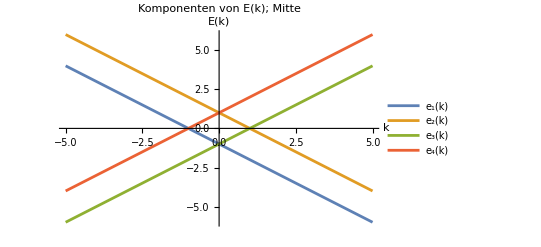

(-μ-k v ℏ==e0
μ-k v ℏ==e0
-μ+k v ℏ==e0
μ+k v ℏ==e0)

((-e0-μ)/(v ℏ)
(-e0+μ)/(v ℏ)
(e0+μ)/(v ℏ)
(e0-μ)/(v ℏ))

(-a0 ⅇ^((ⅈ x (-e0-μ))/(v ℏ))+c0 ⅇ^((ⅈ x (e0+μ))/(v ℏ))
a0 ⅇ^((ⅈ x (-e0-μ))/(v ℏ))+c0 ⅇ^((ⅈ x (e0+μ))/(v ℏ))
-d0 ⅇ^((ⅈ x (e0-μ))/(v ℏ))+b0 ⅇ^((ⅈ x (-e0+μ))/(v ℏ))
d0 ⅇ^((ⅈ x (e0-μ))/(v ℏ))+b0 ⅇ^((ⅈ x (-e0+μ))/(v ℏ)))

```mathematica
MatrixForm[h/. {Δ->0,ϕ->0}]
{vals0,vecs0}=Eigensystem[h/. {Δ->0,ϕ->0}];
vecs0=Transpose[vecs0];
MatrixForm[vals0]
MatrixForm[vecs0]

e0plot[k_]:=vals0;
Plot[Evaluate[e0plot[k]/.{μ->1,v->1, ℏ->1}],{k,-5,5},PlotStyle->ColorData[97,"ColorList"],PlotLegends->Placed[{"e₁(k)","e₂(k)","e₃(k)","e₄(k)"},Right],AxesLabel->{"k","E(k)"},PlotLabel->"Komponenten von E(k); Mitte"]

eqs0=Thread[vals0==ConstantArray[e0,4]];
MatrixForm[eqs0]
k0=Values[Solve[#,k][[1]][[1]]&/@eqs0];
MatrixForm[k0]
ψ0=(vecs0.DiagonalMatrix[{a0,b0,c0,d0}]).E^(I*k0*x);
MatrixForm[ψ0]
```

## Berechnung der Eigenenergien und -funktionen im linken Bereich:

(-μ | k v ℏ | Δ | 0
k v ℏ | -μ | 0 | Δ
Δ | 0 | μ | -k v ℏ
0 | Δ | -k v ℏ | μ)

(-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)
√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)
-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)
√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))

(-(μ-k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(μ-k v ℏ-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(-μ-k v ℏ-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(-μ-k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ
-(μ-k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(μ-k v ℏ-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(μ+k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ | -(μ+k v ℏ-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))/Δ
1 | 1 | -1 | -1
1 | 1 | 1 | 1)

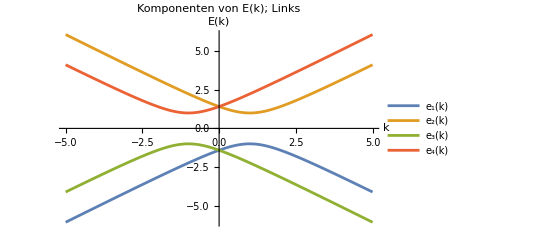

(-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)==eL
√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)==eL
-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)==eL
√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)==eL)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

General::stop: Further output of Solve::nongen will be suppressed during this calculation.

((-√((eL-Δ) (eL+Δ))+μ)/(v ℏ)
(-√((eL-Δ) (eL+Δ))+μ)/(v ℏ)
-(√(eL^2-Δ^2)+μ)/(v ℏ)
-(√(eL^2-Δ^2)+μ)/(v ℏ))

(-(√(eL^2)+√(eL^2-Δ^2))/Δ | (√(eL^2)-√(eL^2-Δ^2))/Δ | (√(eL^2)-√(eL^2-Δ^2))/Δ | -(√(eL^2)+√(eL^2-Δ^2))/Δ
-(√(eL^2)+√(eL^2-Δ^2))/Δ | (√(eL^2)-√(eL^2-Δ^2))/Δ | (-√(eL^2)+√((eL-Δ) (eL+Δ)))/Δ | (√(eL^2)+√(eL^2-Δ^2))/Δ
1 | 1 | -1 | -1
1 | 1 | 1 | 1)

((bL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ+(cL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ-(aL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ-(dL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ
(cL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ)) (-√(eL^2)+√((eL-Δ) (eL+Δ))))/Δ+(bL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ-(aL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ+(dL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ
aL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ))+bL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ))-cL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ))-dL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ))
aL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ))+bL ⅇ^((ⅈ x (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ))+cL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ))+dL ⅇ^(-(ⅈ x (√(eL^2-Δ^2)+μ))/(v ℏ)))

```mathematica
MatrixForm[h/. {ϕ->0}]
{valsL,vecsL}=Eigensystem[h/. {ϕ->0}];
vecsL=Transpose[vecsL];
MatrixForm[valsL]
MatrixForm[vecsL]
eLplot[k_]:=valsL;
Plot[Evaluate[eLplot[k]/.{μ->1,v->1, ℏ->1,Δ->1}],{k,-5,5},PlotStyle->ColorData[97,"ColorList"],PlotLegends->Placed[{"e₁(k)","e₂(k)","e₃(k)","e₄(k)"},Right],AxesLabel->{"k","E(k)"},PlotLabel->"Komponenten von E(k); Links"]
eqsL=Thread[valsL==ConstantArray[eL,4]];
MatrixForm[eqsL]
kL=FullSimplify[Values[Solve[#,k][[1]][[1]]&/@eqsL]];
MatrixForm[kL]
vecsL=Transpose[{FullSimplify[Transpose[vecsL][[1]] /.k->kL[[1]]],FullSimplify[Transpose[vecsL][[2]] /.k->kL[[2]]],FullSimplify[Transpose[vecsL][[3]] /.k->kL[[3]]],FullSimplify[Transpose[vecsL][[4]] /.k->kL[[4]]]}];
MatrixForm[vecsL]
ψL=(vecsL.DiagonalMatrix[{aL,bL,cL,dL}]).E^(I*kL*x);
MatrixForm[ψL]
```

## Berechnung der Eigenenergien und -funktionen im rechten Bereich:

(-μ | k v ℏ | ⅇ^(-ⅈ ϕ) Δ | 0
k v ℏ | -μ | 0 | ⅇ^(-ⅈ ϕ) Δ
ⅇ^(ⅈ ϕ) Δ | 0 | μ | -k v ℏ
0 | ⅇ^(ⅈ ϕ) Δ | -k v ℏ | μ)

(-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)
√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)
-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)
√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2))

(-(ⅇ^(-ⅈ ϕ) (μ-k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | (ⅇ^(-ⅈ ϕ) (-μ+k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | (ⅇ^(-ⅈ ϕ) (μ+k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | -(ⅇ^(-ⅈ ϕ) (-μ-k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ
-(ⅇ^(-ⅈ ϕ) (μ-k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | (ⅇ^(-ⅈ ϕ) (-μ+k v ℏ+√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | -(ⅇ^(-ⅈ ϕ) (μ+k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ | (ⅇ^(-ⅈ ϕ) (-μ-k v ℏ+√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)))/Δ
1 | 1 | -1 | -1
1 | 1 | 1 | 1)

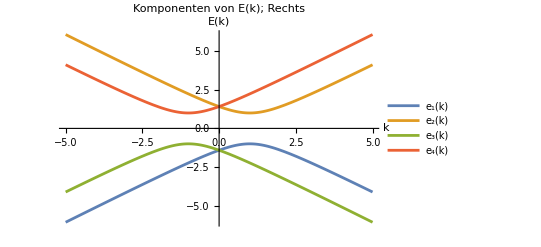

(-√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)==eR
√(Δ^2+μ^2-2 k v μ ℏ+k^2 v^2 ℏ^2)==eR
-√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)==eR
√(Δ^2+μ^2+2 k v μ ℏ+k^2 v^2 ℏ^2)==eR)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

General::stop: Further output of Solve::nongen will be suppressed during this calculation.

((-√((eR-Δ) (eR+Δ))+μ)/(v ℏ)
(-√((eR-Δ) (eR+Δ))+μ)/(v ℏ)
-(√(eR^2-Δ^2)+μ)/(v ℏ)
-(√(eR^2-Δ^2)+μ)/(v ℏ))

(-(ⅇ^(-ⅈ ϕ) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ
-(ⅇ^(-ⅈ ϕ) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ
1 | 1 | -1 | -1
1 | 1 | 1 | 1)

((cR ⅇ^(-ⅈ ϕ+(ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ+(dR ⅇ^(-ⅈ ϕ+(ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ-(aR ⅇ^(-ⅈ ϕ+(ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ+(bR ⅇ^(-ⅈ ϕ+(ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ
(dR ⅇ^(-ⅈ ϕ+(ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ+(cR ⅇ^(-ⅈ ϕ+(ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ-(aR ⅇ^(-ⅈ ϕ+(ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ+(bR ⅇ^(-ⅈ ϕ+(ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ
-cR ⅇ^((ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))-dR ⅇ^((ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))+aR ⅇ^((ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))+bR ⅇ^((ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))
cR ⅇ^((ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))+dR ⅇ^((ⅈ x (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))+aR ⅇ^((ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))+bR ⅇ^((ⅈ x (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)))

```mathematica
MatrixForm[h]
{valsR,vecsR}=Eigensystem[h];
vecsR=Transpose[vecsR];
MatrixForm[valsR]
MatrixForm[vecsR]
eRplot[k_]:=valsR;
Plot[Evaluate[eRplot[k]/.{μ->1,v->1, ℏ->1,Δ->1}],{k,-5,5},PlotStyle->ColorData[97,"ColorList"],PlotLegends->Placed[{"e₁(k)","e₂(k)","e₃(k)","e₄(k)"},Right],AxesLabel->{"k","E(k)"},PlotLabel->"Komponenten von E(k); Rechts"]
eqsR=Thread[valsR==ConstantArray[eR,4]];
MatrixForm[eqsR]
kR=Values[Solve[#,k][[1]][[1]]&/@eqsR];
MatrixForm[FullSimplify[kR]]
vecsR=Transpose[{FullSimplify[Transpose[vecsR][[1]] /.k->kR[[1]]],FullSimplify[Transpose[vecsR][[2]] /.k->(√((eR-Δ) (eR+Δ))+μ)/(v ℏ)],FullSimplify[Transpose[vecsR][[3]] /.k->kR[[3]]],FullSimplify[Transpose[vecsR][[4]] /.k->-(-√(eR^2-Δ^2)+μ)/(v ℏ)]}];
MatrixForm[vecsR]
ψR=(vecsR.DiagonalMatrix[{aR,bR,cR,dR}]).E^(I*kR*x);
MatrixForm[ψR]
```

## Aufstellen der Stetigkeits-Matrix und berechnen der Determinante

```mathematica
gesMatrix=ArrayFlatten[{
{Transpose[Transpose[vecsL]*E^(I*kL*x)],-Transpose[Transpose[vecs0]*E^(I*k0*x)],0}                                      /. {x-> -L},
{0,-Transpose[Transpose[vecs0]*E^(I*k0*x)],Transpose[Transpose[vecsR]*E^(I*kR*x)]}                                     /. {x-> L}
}];
MatrixForm[gesMatrix] 
gesMatrixReduced=Transpose[Delete[Transpose[gesMatrix],{{1},{3},{9},{11}}]];      (*bL->0,dL->0, aR->0, cR-> 0*)
MatrixForm[FullSimplify[gesMatrixReduced]]
determinante=FullSimplify[Det[gesMatrixReduced/.{e0->e, eR->e, eL-> e}]]
 (*Cramersche Regel*)
```

(-(ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ | (ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ | (ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ | -(ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ | ⅇ^(-(ⅈ L (-e0-μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | 0 | 0 | 0 | 0
-(ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ | (ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)-√(eL^2-Δ^2)))/Δ | (ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) (-√(eL^2)+√((eL-Δ) (eL+Δ))))/Δ | (ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) (√(eL^2)+√(eL^2-Δ^2)))/Δ | -ⅇ^(-(ⅈ L (-e0-μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | 0 | 0 | 0 | 0
ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | -ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) | -ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (-e0+μ))/(v ℏ)) | 0 | ⅇ^(-(ⅈ L (e0-μ))/(v ℏ)) | 0 | 0 | 0 | 0
ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | ⅇ^(-(ⅈ L (-√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) | ⅇ^((ⅈ L (√(eL^2-Δ^2)+μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (-e0+μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0-μ))/(v ℏ)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ L (-e0-μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | -(ⅇ^(-ⅈ ϕ+(ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ
0 | 0 | 0 | 0 | -ⅇ^((ⅈ L (-e0-μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | -(ⅇ^(-ⅈ ϕ+(ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ ϕ+(ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ
0 | 0 | 0 | 0 | 0 | -ⅇ^((ⅈ L (-e0+μ))/(v ℏ)) | 0 | ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | ⅇ^((ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | ⅇ^((ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | -ⅇ^((ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | -ⅇ^((ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2))
0 | 0 | 0 | 0 | 0 | -ⅇ^((ⅈ L (-e0+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | ⅇ^((ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | ⅇ^((ⅈ L (v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | ⅇ^((ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)) | ⅇ^((ⅈ L (-v μ ℏ-√(eR^2 v^2 ℏ^2-v^2 Δ^2 ℏ^2)))/(v^2 ℏ^2)))

((ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))-μ))/(v ℏ)) (√(eL^2)-√((eL-Δ) (eL+Δ))))/Δ | -(ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√((eL-Δ) (eL+Δ))))/Δ | ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | 0 | 0
(ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))-μ))/(v ℏ)) (√(eL^2)-√((eL-Δ) (eL+Δ))))/Δ | (ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) (√(eL^2)+√((eL-Δ) (eL+Δ))))/Δ | -ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | 0 | 0
ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))-μ))/(v ℏ)) | -ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | 0 | ⅇ^(-(ⅈ L (e0-μ))/(v ℏ)) | 0 | 0
ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))-μ))/(v ℏ)) | ⅇ^((ⅈ L (√((eL-Δ) (eL+Δ))+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | 0 | -ⅇ^(-(ⅈ L (e0-μ))/(v ℏ)) | 0 | 0
0 | 0 | ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | (ⅇ^(-ⅈ (ϕ+(L (√(eR^2-Δ^2)-μ))/(v ℏ))) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ (ϕ+(L (√(eR^2-Δ^2)+μ))/(v ℏ))) (-√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ
0 | 0 | -ⅇ^(-(ⅈ L (e0+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0+μ))/(v ℏ)) | 0 | (ⅇ^(-ⅈ (ϕ+(L (√(eR^2-Δ^2)-μ))/(v ℏ))) (√(eR^2)+√((eR-Δ) (eR+Δ))))/Δ | (ⅇ^(-ⅈ (ϕ+(L (√(eR^2-Δ^2)+μ))/(v ℏ))) (√(eR^2)-√((eR-Δ) (eR+Δ))))/Δ
0 | 0 | 0 | -ⅇ^((ⅈ L (-e0+μ))/(v ℏ)) | 0 | ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | ⅇ^(-(ⅈ L (√((eR-Δ) (eR+Δ))-μ))/(v ℏ)) | -ⅇ^(-(ⅈ L (√((eR-Δ) (eR+Δ))+μ))/(v ℏ))
0 | 0 | 0 | -ⅇ^((ⅈ L (-e0+μ))/(v ℏ)) | 0 | -ⅇ^((ⅈ L (e0-μ))/(v ℏ)) | ⅇ^(-(ⅈ L (√((eR-Δ) (eR+Δ))-μ))/(v ℏ)) | ⅇ^(-(ⅈ L (√((eR-Δ) (eR+Δ))+μ))/(v ℏ)))

(32 ⅇ^(-ⅈ ϕ) (Δ^2 Cos[ϕ]+(-2 e^2+Δ^2) Cos[(4 e L)/(v ℏ)]+2 ⅈ √(e^2) √((e-Δ) (e+Δ)) Sin[(4 e L)/(v ℏ)]))/Δ^2

{{e→-Δ √(Cos[ϕ/2]^2)},{e→Δ √(Cos[ϕ/2]^2)}}

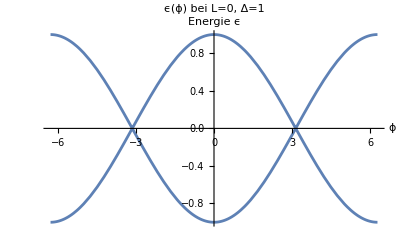

```mathematica
sol1=FullSimplify[Solve[FullSimplify[determinante==0/.L->0],e]]
Plot[(e/. sol1/.Δ->1),{ϕ,-2 π,2 π},PlotRange->All,AxesLabel->{"ϕ","Energie ϵ"},PlotLabel->"ϵ(ϕ) bei L=0, Δ=1"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-ArcCos[-((-2 e^2+Δ^2) Cos[(4 e L)/(v ℏ)]+2 ⅈ √(e^2) √((e-Δ) (e+Δ)) Sin[(4 e L)/(v ℏ)])/Δ^2]},{ϕ→ArcCos[-((-2 e^2+Δ^2) Cos[(4 e L)/(v ℏ)]+2 ⅈ √(e^2) √((e-Δ) (e+Δ)) Sin[(4 e L)/(v ℏ)])/Δ^2]}}

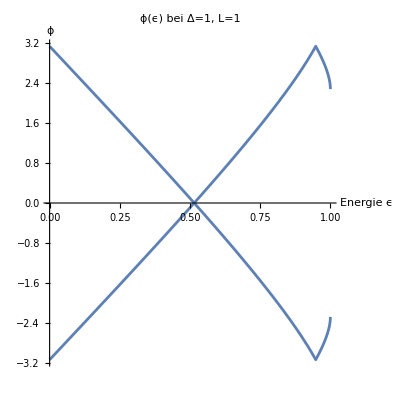

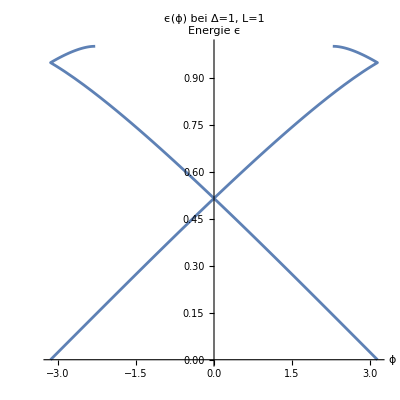

```mathematica
sol2=FullSimplify[Solve[FullSimplify[determinante==0],ϕ]]
Bandlücke=1;
Plot[(ϕ/. sol2/.{Δ->Bandlücke,ℏ->1,v->1,L->1}),{e,0,Bandlücke},PlotRange->All,AxesLabel->{"Energie ϵ","ϕ"},PlotLabel->"ϕ(ϵ) bei Δ=1, L=1",AspectRatio->1]
ParametricPlot[Evaluate[{
{ϕ/. sol2[[1]]/. {Δ->Bandlücke,ℏ->1,v->1,L->1},e},
{ϕ/. sol2[[2]]/. {Δ->Bandlücke,ℏ->1,v->1,L->1},e}
}],
{e,0,Bandlücke},PlotRange->All,AxesLabel->{"ϕ","Energie ϵ"},PlotLabel->"ϵ(ϕ) bei Δ=1, L=1",AspectRatio->1,PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798]} ]
```